### First step

```mathematica
Clear[all];
uu=List[-SubStar[u],+SubStar[u]];
```

```mathematica
sol1=Flatten[Simplify[DSolve[{θ'[x]==ω[x],ω'[x]==m[x]+θ[x],m'[x]==uu[[1]],θ[0]==1,ω[0]==Subscript[Ω, 0],m[0]==0},{θ[x],ω[x],m[x]},x],Element[x,Reals]]]
```

{m[x]→-x u_*,θ[x]→1/2 ⅇ^-x (1+ⅇ^(2 x)+(-1+ⅇ^(2 x)) Ω_0+(1-ⅇ^(2 x)+2 ⅇ^x x) u_*),ω[x]→1/2 ⅇ^-x ((1+ⅇ^(2 x)) Ω_0-(-1+ⅇ^x) (-1-ⅇ^x+(-1+ⅇ^x) u_*))}

```mathematica
linkingStage1={m[x]/.sol1⟦1⟧/.x->Subscript[τ, 1],θ[x]/.sol1⟦2⟧/.x->Subscript[τ, 1],ω[x]/.sol1⟦3⟧/.x->Subscript[τ, 1]}
```

{-τ_1 u_*,1/2 ⅇ^-τ_1 (1+ⅇ^(2 τ_1)+(-1+ⅇ^(2 τ_1)) Ω_0+(1-ⅇ^(2 τ_1)+2 ⅇ^τ_1 τ_1) u_*),1/2 ⅇ^-τ_1 ((1+ⅇ^(2 τ_1)) Ω_0-(-1+ⅇ^τ_1) (-1-ⅇ^τ_1+(-1+ⅇ^τ_1) u_*))}

```mathematica
sol2=Simplify[DSolve[{θ'[x]==ω[x],ω'[x]==m[x]+θ[x],m'[x]==uu[[2]],θ[Subscript[τ, f]]==0,ω[Subscript[τ, f]]==0,m[Subscript[τ, f]]==0},{θ[x],ω[x],m[x]},x],Element[{Subscript[τ, 1],Subscript[τ, 2],Subscript[τ, f],x},Reals]]//Flatten
```

{m[x]→(x-τ_f) u_*,θ[x]→1/2 (ⅇ^(x-τ_f)-ⅇ^(-x+τ_f)-2 x+2 τ_f) u_*,ω[x]→1/2 ⅇ^(-x-τ_f) (ⅇ^x-ⅇ^τ_f)^2 u_*}

```mathematica
linkingStage2={m[x]/.sol2⟦1⟧/.x->Subscript[τ, 1],θ[x]/.sol2⟦2⟧/.x->Subscript[τ, 1]//Simplify,ω[x]/.sol2⟦3⟧/.x->Subscript[τ, 1]//Simplify}
```

{(τ_1-τ_f) u_*,1/2 (ⅇ^(τ_1-τ_f)-ⅇ^(-τ_1+τ_f)-2 τ_1+2 τ_f) u_*,1/2 ⅇ^(-τ_1-τ_f) (ⅇ^τ_1-ⅇ^τ_f)^2 u_*}

### Full system

```mathematica
first=(linkingStage1[[1]]-linkingStage2[[1]]==0//FullSimplify)
second=(linkingStage1[[2]]-linkingStage2[[2]]==0//Simplify)
third=(linkingStage1[[3]]-linkingStage2[[3]]==0//Simplify)
```

2 τ_1 u_*==τ_f u_*

ⅇ^-τ_1+ⅇ^τ_1+(-ⅇ^-τ_1+ⅇ^τ_1) Ω_0+(ⅇ^(-τ_1-τ_f) (1+ⅇ^τ_f) (-ⅇ^(2 τ_1)+ⅇ^τ_f)+4 τ_1-2 τ_f) u_*==0

ⅇ^-τ_1+(-4+ⅇ^-τ_1+ⅇ^τ_1+ⅇ^(τ_1-τ_f)+ⅇ^(-τ_1+τ_f)) u_*==ⅇ^τ_1+(ⅇ^-τ_1+ⅇ^τ_1) Ω_0

### Make variable replace ⅇ^τ_1=x ; ⅇ^τ_f=z

```mathematica
first1=(x^2==z)
Collect[second/.{ⅇ^Subscript[τ, 1]->x,ⅇ^Subscript[τ, f]->z,ⅇ^(-Subscript[τ, 1])->1/x,ⅇ^(-3 Subscript[τ, 1])->1/x^3,Subscript[τ, f]->2 Subscript[τ, 1]}//Simplify,{ⅇ^Subscript[τ, f],ⅇ^Subscript[τ, 1]},FullSimplify]
Collect[third/.{ⅇ^Subscript[τ, 1]->x,ⅇ^Subscript[τ, f]->z,ⅇ^(-Subscript[τ, 1])->1/x,ⅇ^(-3 Subscript[τ, 1])->1/x^3,Subscript[τ, f]->2 Subscript[τ, 1]}//Simplify,{ⅇ^Subscript[τ, f],ⅇ^Subscript[τ, 1]},FullSimplify]
```

x^2==z

(1+x^2+(-1+x^2) Ω_0)/x-ⅇ^-τ_1 (1+z) u_*+ⅇ^(-3 τ_1) z (1+z) u_*==0

ⅇ^-τ_1 u_*+ⅇ^τ_1 u_*+(1+u_*+(-4+x) x u_*)/x==x+(1/x+x) Ω_0

```mathematica
second1=((1+x^2+(-1+x^2) Subscript[Ω, 0])/x-1/x (1+z) SubStar[u]+1/x^3 z (1+z) SubStar[u]==0)//Simplify
third1=(1/x SubStar[u]+x* SubStar[u]+(1+SubStar[u]+(-4+x) x SubStar[u])/x==x+(1/x+x) Subscript[Ω, 0])//Simplify
```

x+x^3+x (-1+x^2) Ω_0==((x^2-z) (1+z) u_*)/x

(1+2 (-1+x)^2 u_*)/x==x+(1/x+x) Ω_0

```mathematica
Together[Collect[second1,{x}]]
Together[Collect[third1,{z}]]
```

x+x^3-x Ω_0+x^3 Ω_0==(x^2 u_*-z u_*+x^2 z u_*-z^2 u_*)/x

(1+2 u_*-4 x u_*+2 x^2 u_*)/x==(x^2+Ω_0+x^2 Ω_0)/x

```mathematica
SubStar[t]=0.174; Subscript[ω, 0]=0.149;Subscript[ϕ, 0]=0.021;SubStar[u]=7;Subscript[Ω, 0]=SubStar[t]/Subscript[ϕ, 0] Subscript[ω, 0];l=0.88;
Print["Ω_0=",Subscript[Ω, 0]];
```

Ω_0=1.23457

Ω_0=1.23457

Ω_0=1.23457

«1 more identical outputs»

```mathematica
(*Solve[third1&&second1,{x,z},Reals]*)
 roots=NSolve[third1&&second1&&z>1,{x,z},Reals]//Flatten
```

{x→1.68585,z→2.01973}

```mathematica
Subscript[τ, 1]=Log[roots[[1]][[2]]];Subscript[τ, f]=Log[roots[[2]][[2]]];
Print["t1=",SubStar[t]*Subscript[τ, 1],"; tf=",SubStar[t]*Subscript[τ, f]]
Print["τ1=",Subscript[τ, 1],"; τf=",Subscript[τ, f]]
```

t1=0.0908746; tf=0.122316

τ1=0.522268; τf=0.702964

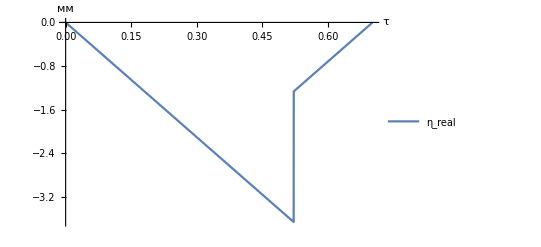

{0.,-18.9399,-19.4062,-19.8783,-20.3553,-20.8362,-21.3203,-21.8067,-22.2946,-22.7831,-23.2715,-23.7588,-24.2442,-24.7269,-25.206,-25.6807,-26.1502,-26.6135,-27.07,-27.5186,-27.9586,-28.389,-28.8091,-29.2179,-29.6146,-29.9984,-30.3682,0.0934338,0.0630633,0.0401159,0.0235473,0.0123161,0.00538296,0.00171008,0.000261114,5.61683×10^-7}

./Study/kursach_MUS/file2.mat

```mathematica
pw1θ=Piecewise[{{sol1[[2]][[2]],x>0&&x<=Subscript[τ, 1]},{sol2[[2]][[2]],x>Subscript[τ, 1]&&x<=Subscript[τ, f]}}];
pw1m=Piecewise[{{sol1[[1]][[2]],x>0&&x<=Subscript[τ, 1]},{sol2[[1]][[2]],x>Subscript[τ, 1]&&x<=Subscript[τ, f]}}];
pw1θreal=-l*1000*Subscript[ϕ, 0]*pw1θ;
Plot[{pw1m},{x,0,Subscript[τ, f]},AxesLabel->{Style["τ",17,Black],Style["мм",17,Black]},PlotLegends->{"η_real"}]
Table[pw1θreal,{x,0,Subscript[τ, f],0.02}]
Export["./Study/kursach_MUS/file2.mat",{"optEta"->{Table[pw1θreal,{x,0,Subscript[τ, f],0.02}]},"tf"->SubStar[t]*Subscript[τ, f],"tauf"->Subscript[τ, f],"uast"->SubStar[u]},"LabeledData"]
```